```mathematica
NotebookDirectory[]
```

/Users/pbialas/PET/tools/gate_input/

```mathematica
w=0.006
h=0.024
wMod = 13*w+0.007
hMod=  h+0.001
```

0.006

0.024

0.085

0.025

```mathematica
R=.
```

```mathematica
phi = 2*ArcTan[R, wMod/2]
```

2 ArcTan[R,0.0425]

```mathematica
Pi/12.0
```

0.261799

```mathematica
Solve[2ArcTan[r, wMod/2]==Pi/12,r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→0.32282}}

```mathematica
R=0.34
```

0.34

```mathematica
mod=Rectangle[-1/2{hMod,wMod},1/2{hMod,wMod}]
```

Rectangle[{-0.012,-0.039},{0.012,0.039}]

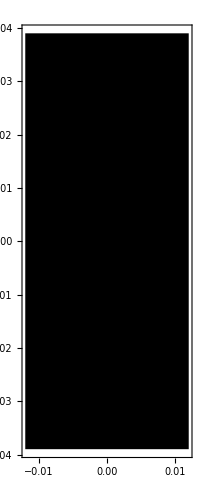

```mathematica
Graphics[mod, Frame->True]
```

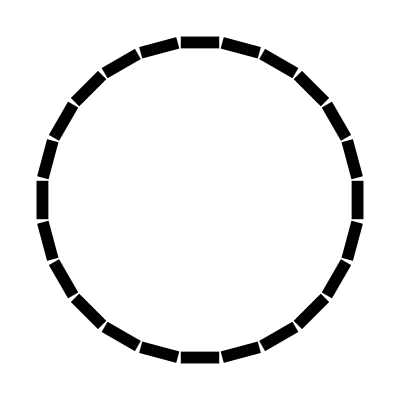

```mathematica
Graphics[Table[Rotate[Translate[mod,{-R,0}],Pi/12 *i ,{0,0}],{i,0,23} ]]
```

```mathematica
Graphics[Rotate[Translate[mod,{-R,0}],Pi/12 ],Frame->True]
```

-Graphics-